0.2

0.8

5.9368

0.028+NoV

1.32 2^(-10.3 NoV) (1-ⅇ^(-5.9368 (0.028+NoV)))

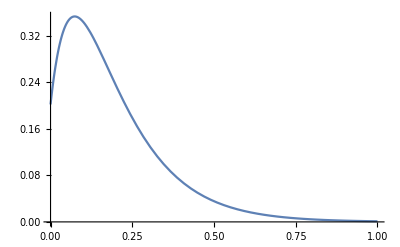

```mathematica
(* accurate a0 *)

Roughness=0.2
glossness=1-Roughness
a0t1=11.4  * glossness^3+0.1
a0t2=NoV+(0.1-0.09  *glossness)
codAccurateA0 =(1 - E^(-a0t1*a0t2))*1.32*2^(-10.3*NoV)
Plot[codAccurateA0,{NoV,0,1}]
```

```mathematica
(* accurate a1 *)
```

1

9.2136

0.045+NoV

Min[1,1-2^(-9.2136 (0.045+NoV))]

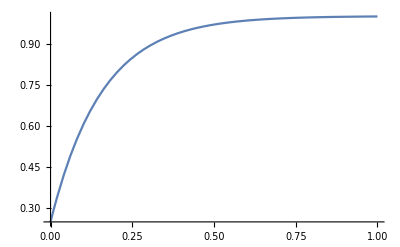

```mathematica
a1t1=Max[(1.336 - 0.486 * glossness),1]
a1t2 = 0.06+3.25*glossness+12.8 * glossness^3
a1t3=NoV+Min[(0.125-0.1 *glossness),0.1]
codAccurateA1 =Min[ a1t1 - 2^(-a1t2 * a1t3) ,1]
Plot[codAccurateA1,{NoV,0,1}]
```